```mathematica
(*Mathematica*)
```

```mathematica
(* border plot of Cubic Julia Centiped Longbrot set*)
```

```mathematica
Export["centipipede.jpg",ListPlot[JuliaSetPoints[-0.5390625+0.7367187500000001 x+3.9890625 x^2+5.04921875 x^3+5.6781250000000005 x^4+4.3125 x^5+1.15 x^6,x],ColorFunction->"Rainbow",ImageSize->2000,PlotStyle->PointSize[0.001]]]
```

centipipede.jpg

```mathematica
jc=JuliaSetPoints[-0.5390625+0.7367187500000001 x+3.9890625 x^2+5.04921875 x^3+5.6781250000000005 x^4+4.3125 x^5+1.15 x^6,x];
```

```mathematica
Length[jc]
```

16121

```mathematica
jcc=Table[jc[[i,1]]+I*jc[[i,2]],{i,Length[jc]}];
```

```mathematica
(* box counting program*)
```

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=Block[{tmp,delta,nmax,l,i},tmp={};
delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];
Do[{l=Length[Complement[Ceiling[list/delta],{}]];
AppendTo[tmp,{delta,l}];
delta=delta*scale},{i,1,nmax}];
Return[tmp]];
```

```mathematica
a2=BoxCount[jcc,1.0,0.5,0.01]
```

{{1.,12},{0.5,22},{0.25,48},{0.125,126},{0.0625,343},{0.03125,889},{0.015625,2366}}

```mathematica
b2=Table[{Log[a2[[i,1]]],N[Log[a2[[i,2]]]]},{i,Length[a2]}]
```

{{0.,2.48491},{-0.693147,3.09104},{-1.38629,3.8712},{-2.07944,4.83628},{-2.77259,5.83773},{-3.46574,6.7901},{-4.15888,7.76896}}

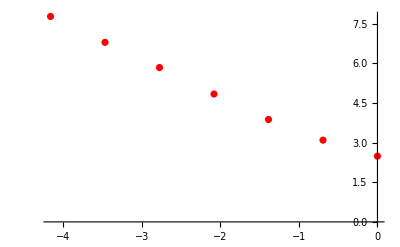

```mathematica
g1=ListPlot[b2,PlotStyle->Red]
```

```mathematica
g[x_]=Fit[b2,{1,x},x]
```

2.25252-1.29929 x

```mathematica
(* fractal dimension Cubic Julia longbrot set border*)
```

```mathematica
s0=-CoefficientList[g[x],x][[2]]
```

1.29929

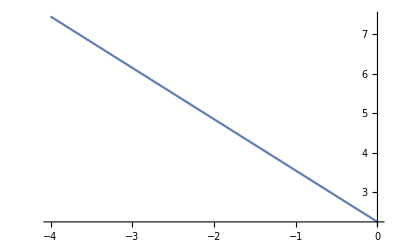

```mathematica
g2=Plot[g[x],{x,-4,0}]
```

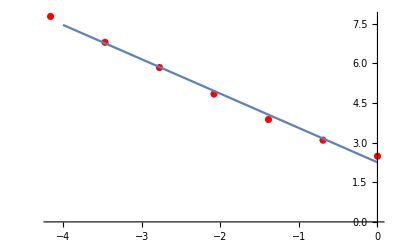

```mathematica
Show[{g1,g2}]
```

```mathematica
(* end*)
```